# Fitting a hexagonal grid to points

## Tao Ju (2021) C++ In mathematica (Run?)

I’m not sure if this section is necessary for the c++ code. Do I start with a perfectly hexagonal grid? If I’m doing the importing within my own code, I may not need to manually adjust the hex grid to match because the algorithm would be able to do that itself.

## Code

Given a set of points that roughly lie on a hexagonal grid, this algorithm tries to fit the best grid to them. The grid is represented as a tuple {origin, vec} where vec forms a hexagonal basis with its 60-degrees-rotated version (magnitude of vec is the distance between two closest grid points). In addition, we produce, for each input point, an integer pair of “coordinates” on this grid.

The algorithm proceeds in two phases:

1. Compute initial grid. I use the RANSAC approach: randomly pick a point as origin,  use its closest neighbor to define the basis, and evaluate the “fit” of the grid to the rest of the points. The “fit” is defined as the number of “inliers”, points within a given distance threshold to some grid point. The best-fit grid is then chosen from the random set.

2. Refine the grid. I use an alternating optimization to update either (1) the origin and vector, or (2) the list of inliers and their grid coordinates, with the goal of maximizing the number of inliers and minimizing their deviation from the grid.

Criteria for inliers (as fraction of one grid unit):

```mathematica
ϵ=0.2;
```

### Helpers

Rotation matrix

This line defines a function to produce arbitrary rotations. The next provides a specifically hex rotation of π/3 radians.

```mathematica
rotM[a_]:=N[{{Cos[a],-Sin[a]},{Sin[a],Cos[a]}}];
hexM=N[rotM[π/3]];
```

### Initial grid

This function computes the (floating point) coordinates of a point pt in the hexagonal basis {origin, v1, v2}:

```mathematica
getCoords[pt_,origin_,v1_,v2_]:=Inverse[Transpose[{v1,v2}]].(pt-origin);
```

This function computes the X,Y coordinates of a point with coordinates coords in the hexagonal grid:

```mathematica
getPt[coords_,origin_,v1_,v2_]:=coords.{v1,v2}+origin;
```

```mathematica
getPt[getCoords[{-1,3},{0,0},{1,0},hexM.{1,0}],{0,0},{1,0},hexM.{1,0}]
```

{-1.,3.}

This function takes the input points pts and a basis {origin, vec} and outputs the indices of those in pts that are within ϵ*|vec| from a grid point and the integer coordinates of that grid point.

```mathematica
getInliers[pts_,{origin_,vec_}]:=Module[{intcoords,vec2=hexM.vec,inds},
intcoords=Map[Round[getCoords[#,origin,vec,vec2]]&,pts];
inds=Select[Range[Length[pts]],(Norm[pts⟦#⟧-getPt[intcoords⟦#⟧,origin,vec,vec2]]<ϵ*Norm[vec])&];
{inds,intcoords⟦inds⟧}];
```

The RANSAC algorithm on points pts for num number of random picks, producing an initial grid and the corresponding inliers:

```mathematica
initGridInliers[pts_,num_]:=Module[{ori,v,in={{},{}},oriTemp,vTemp,inTemp},
Do[oriTemp=RandomSample[pts,1]⟦1⟧;
vTemp=Nearest[pts,oriTemp,2]⟦2⟧-oriTemp;
inTemp=getInliers[pts,{oriTemp,vTemp}];
If[Length[inTemp⟦1⟧]>Length[in⟦1⟧],
ori=oriTemp;
v=vTemp;
in=inTemp],
{i,num}];
{{ori,v},in}];
```

### Grid refinement

The origin o, a basis (column) vector v, rotation matrix R to obtain the second basis, and grid coordinates {a,b}, the location of the point is expressed as:

a*v+b*R·v+o
=a*I·v+b*R·v+o
=(a*I+b*R)·v+o
=(a*I+b*R, | I)(v
o)

where I is the 2x2 identity matrix. Given grid coordinates {a_i,b_i}, we wish to find origin/vector pair {o,v} that best approximates target locations {p_i} in the least-square sense:

∑_i ((a_i*I+b_i*R, | I)(v
o)-p_i)^2

Re-writing it in matrix form as:

(A·(v
o)-B)^2, A=(a_1*I+b_1*R, | I
a_2*I+b_2*R, | I
⋮ | ⋮), B=(p_1
p_2
⋮)

The minimizer is computed as:

(v
o)=(A^T A)^-1(A^T B)

Based on the derivation above, this function takes a set of inliers and their grid coordinates, and computes the optimal grid {origin,vec} that best matches the inliers:

```mathematica
getGrid[pts_,{inds_,intcoords_}]:=Module[{ata=Table[0,{4},{4}],atb=Table[0,{4}],a,I2=IdentityMatrix[2],res},
Do[a=Transpose[Join[Transpose[intcoords⟦i,1⟧*I2+intcoords⟦i,2⟧*hexM],I2]];
ata+=Transpose[a].a;
atb+=Transpose[a].pts⟦inds⟦i⟧⟧,
{i,Length[inds]}];
res=Inverse[ata].atb;
{res⟦{3,4}⟧,res⟦{1,2}⟧}];
```

This function iterates between grid refinement and finding inliers, until the number of inliers does not increase.

```mathematica
refineGrid[pts_,grid_,inliers_]:=Module[{ng=grid,ni=inliers,num=Length[inliers⟦1⟧]},
While[num<Length[pts],
(* Print["Iterate"]; *)
ng=getGrid[pts,ni];
ni=getInliers[pts,ng];
If[Length[ni⟦1⟧]>num,
num=Length[ni⟦1⟧],
Break[]]];
ng=getGrid[pts,ni];
{ng,ni}];
```

### Putting together

Finally, this function combines both phases (taking num of RANSAC iterations), and outputs the grid and integer coordinates for every point:

```mathematica
getGridAndCoords[pts_,num_]:=Module[{grid,inliers,v2},
{grid,inliers}=initGridInliers[pts,num];
{grid,inliers}=refineGrid[pts,grid,inliers];
v2=hexM.grid⟦2⟧;
{grid,Map[Round[getCoords[#,grid⟦1⟧,grid⟦2⟧,v2]]&,pts]}];
```

### Utilities

This function takes in a set of points pts, another set of points samples to “cover”,  a buffer width wid, and num of RANSAC iterations, expands the given points to cover the samples and grow the buffer. Returns the list of new points.

```mathematica
growAndCover[pts_,samples_,wid_,num_]:=Module[{hash,ncoords={},grid,coords,loc,nghbs={{1,0},{0,1},{-1,1},{-1,0},{0,-1},{1,-1}},nghbs2,v2,bd,nbd},
(* Compute grid and coordinates *)
{grid,coords}=getGridAndCoords[pts,num];
v2=hexM.grid⟦2⟧;

(* Store existing points in hash *)
hash[_,_]=False;
Scan[(hash[#⟦1⟧,#⟦2⟧]=True)&,coords];

(* for each sample, if its nearest grid point and or any of its 6-neighbors are not in the list, add them to the list *)
nghbs2=Append[nghbs,{0,0}];
Scan[
(loc=Round[getCoords[#,grid⟦1⟧,grid⟦2⟧,v2]];
Scan[If[!(Apply[hash,loc+#]),
hash[loc⟦1⟧+#⟦1⟧,loc⟦2⟧+#⟦2⟧]=True;
AppendTo[ncoords,loc+#]]&,nghbs2])&,
samples];

(* growing *)
bd=Join[coords,ncoords]; (* queue of points added in the previous iteration *)
Do[
nbd={}; (* queue of points added in this iteration *)
Scan[
(loc=#;
Scan[If[!(Apply[hash,loc+#]),
hash[loc⟦1⟧+#⟦1⟧,loc⟦2⟧+#⟦2⟧]=True;
AppendTo[ncoords,loc+#];
AppendTo[nbd,loc+#]]&,nghbs])&,
bd];
bd=nbd,
{i,wid}];

Map[getPt[#,grid⟦1⟧,grid⟦2⟧,v2]&,ncoords]];
```

### Drawing

Getting the range of a point set with an expansion ratio r (r=1 means no expansion):

```mathematica
getRangeRatio[pts_,r_]:=Map[{(1-r)Mean[#]+r#⟦1⟧,(1-r)Mean[#]+r#⟦2⟧}&,Transpose[{Map[Min,Transpose[pts]],Map[Max,Transpose[pts]]}]];
```

Draws input points pts, the grid defined by {origin, vec}, and the inliers {inliers,intcoords}:

```mathematica
drawFit[pts_,{origin_,vec_},{inds_,intcoords_},ptSize_]:=Module[{r=getRangeRatio[pts,1.2],outinds=Complement[Range[Length[pts]],inds],rcoords,lx,hx,ly,hy,vec2=hexM.vec},
rcoords=Map[Round[getCoords[#,origin,vec,vec2]]&,{{r⟦1,1⟧,r⟦2,1⟧},{r⟦1,1⟧,r⟦2,2⟧},{r⟦1,2⟧,r⟦2,1⟧},{r⟦1,2⟧,r⟦2,2⟧}}];
{lx,ly}=Map[Min,Transpose[rcoords]];
{hx,hy}=Map[Max,Transpose[rcoords]];

Graphics[{
(* outlier points *)
{Red, AbsolutePointSize[ptSize],Map[Point,pts⟦outinds⟧]},
(* inlier points *)
{Green, AbsolutePointSize[ptSize],Map[Point,pts⟦inds⟧]},
(* grid *)
{Black, AbsolutePointSize[ptSize*2],Point[origin]},
{Black,AbsoluteThickness[ptSize],Line[{origin,origin+vec}]},
{LightGray,Table[Line[{getPt[{x,ly},origin,vec,vec2],getPt[{x,hy},origin,vec,vec2]}],{x,lx,hx}],
Table[Line[{getPt[{lx,y},origin,vec,vec2],getPt[{hx,y},origin,vec,vec2]}],{y,ly,hy}]},
(* inlier grid points *)
{Blue,AbsolutePointSize[ptSize],Map[Point[getPt[#,origin,vec,vec2]]&,intcoords]}},
PlotRange->r]];
```

## Test

### Generate test points

Generate a hex grid with dimension n×m and spacing len, whose lower-left corner is at lowleft, with rotation angle rot, missing point probability prob, and perturbation pert:

```mathematica
perturb[pts_,e_]:=Map[(Map[(#+RandomReal[{-e,e}])&,#])&,pts];
```

```mathematica
genHexGrid2D[n_,m_,len_,lowleft_,rot_,prob_,pert_]:=Module[{h=len*√3/2,pts,rM=rotM[rot],res},
res=perturb[N[Flatten[Table[If[OddQ[i],
(* long line *)
Table[rM.{(j-1)*len,(i-1)*h}+lowleft,{j,n}],
(* short line *)
Table[rM.{(j-.5)*len,(i-1)*h}+lowleft,{j,n-1}]],{i,m}],1]],pert];
Pick[res,Map[(RandomReal[]>prob)&,res]]];
```

### Test 1

#### Input

```mathematica
cols=10;
rows=10;
corner={0,0};
spacing=1.0;
rot=0.2;
missingprob=0.3;
perturbation=0.15;
SeedRandom[0];
pts=genHexGrid2D[cols,rows,spacing,corner,rot,missingprob,perturbation];
```

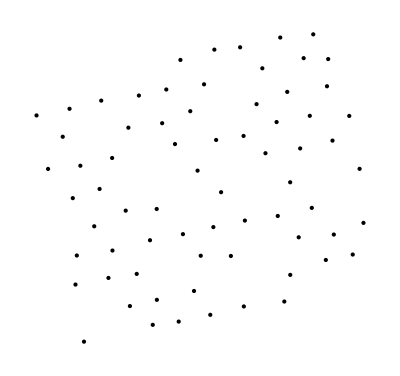

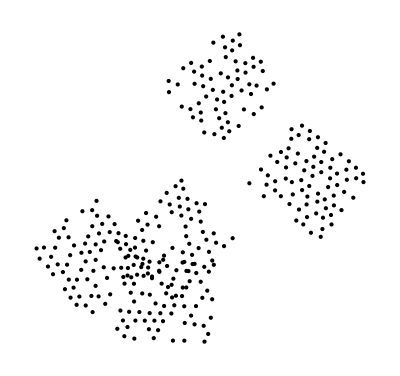

C:\Users\Aiden McIlraith\Documents\GitHub\st-visualizer\growTests.json

```mathematica
Graphics[Map[Point,pts]]
genPts =Map[(genHexGrid2D[cols,rows,spacing,{RandomReal[{-10,10}],RandomReal[{-10,10}]},RandomReal[{0,2*π}],missingprob,perturbation])&,Range[5]];
Graphics[Map[Point,genPts]]
Export["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\growTests.json",genPts]
```

#### Randomly select origin/vec

```mathematica
origin=RandomSample[pts,1]⟦1⟧;
vec=Nearest[pts,origin,2]⟦2⟧-origin;
grid={origin,vec};
Norm[vec]
```

0.928198

```mathematica
inliers=getInliers[pts,grid];
```

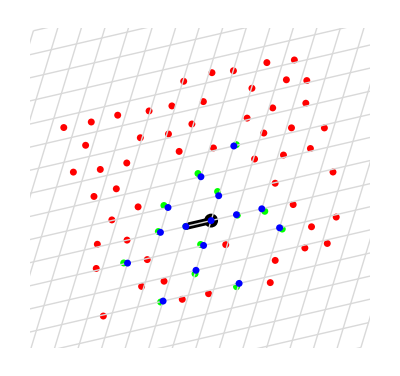

```mathematica
drawFit[pts,grid,inliers,5]
```

#### RANSAC

```mathematica
SeedRandom[0];
```

```mathematica
{grid,inliers}=initGridInliers[pts,20];
```

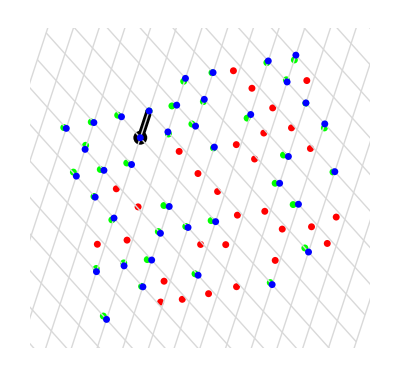

```mathematica
drawFit[pts,grid,inliers,5]
```

```mathematica
grid2=getGrid[pts,inliers];
inliers2=getInliers[pts,grid2];
```

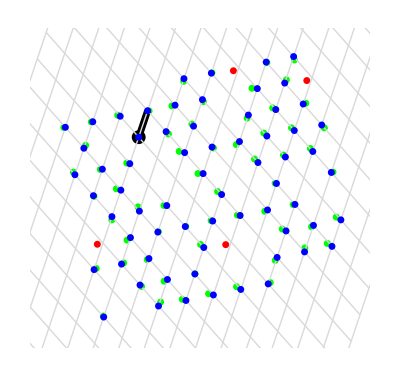

```mathematica
drawFit[pts,grid2,inliers2,5]
```

```mathematica
grid3=getGrid[pts,inliers2];
inliers3=getInliers[pts,grid3];
```

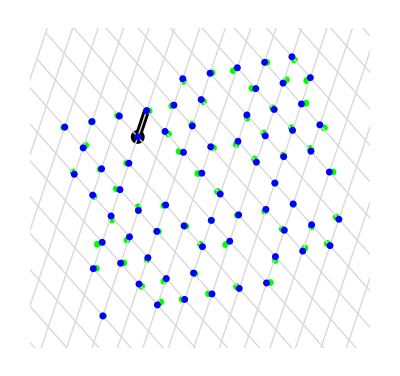

```mathematica
drawFit[pts,grid3,inliers3,5]
```

#### Refinement

```mathematica
{ngrid,ninliers}=refineGrid[pts,grid,inliers];
```

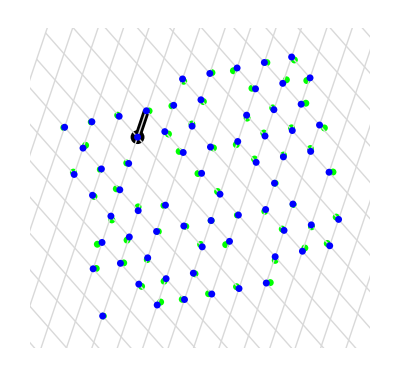

```mathematica
drawFit[pts,ngrid,ninliers,5]
```

#### Full pipeline

```mathematica
SeedRandom[0];
```

```mathematica
{grid,coords}=getGridAndCoords[pts,20];
```

```mathematica
drawFit[pts,grid,{Range[Length[pts]],coords},5]
```

-Graphics-

#### Cover and grow

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts0=growAndCover[pts,samples,0,50];
```

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts1=growAndCover[pts,samples,1,50];
```

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts2=growAndCover[pts,samples,2,50];
```

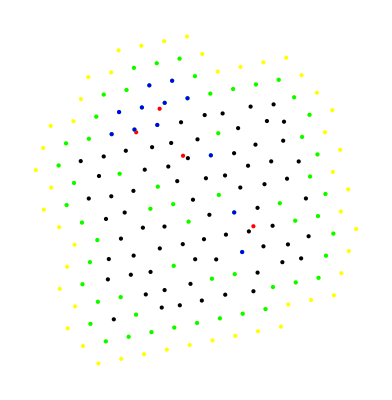

```mathematica
Graphics[{Map[Point,pts],{Red,Map[Point,samples]},{Yellow,Map[Point,npts2]},{Green,Map[Point,npts1]},{Blue,Map[Point,npts0]}}]
```

### Test 2: NMK_F_U2

#### Input

```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
```

```mathematica
pts=<<"NMK_F_U1_coords.dat";
```

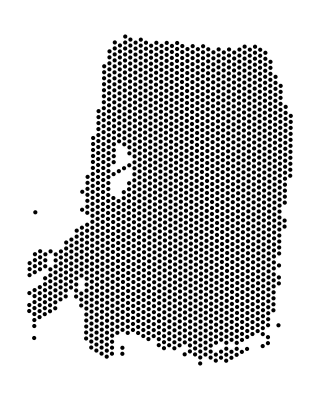

```mathematica
Graphics[Map[Point,pts]]
```

#### Randomly select origin/vec

```mathematica
origin=RandomSample[pts,1]⟦1⟧;
vec=Nearest[pts,origin,2]⟦2⟧-origin;
grid={origin,vec};
Norm[vec]
```

24.9467

```mathematica
inliers=getInliers[pts,grid];
```

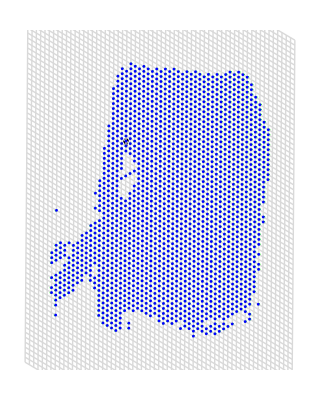

```mathematica
drawFit[pts,grid,inliers,2]
```

#### RANSAC + manual iterative refinment

```mathematica
SeedRandom[0];
```

```mathematica
{grid,inliers}=initGridInliers[pts,5];
```

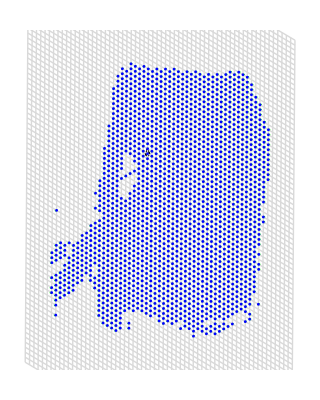

```mathematica
drawFit[pts,grid,inliers,2]
```

```mathematica
grid2=getGrid[pts,inliers];
inliers2=getInliers[pts,grid2];
```

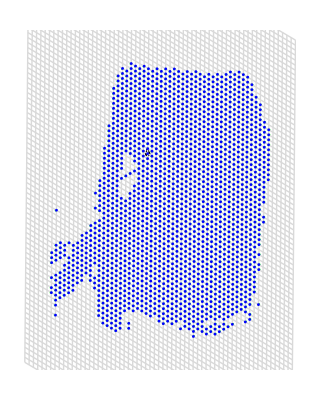

```mathematica
drawFit[pts,grid2,inliers2,2]
```

```mathematica
grid3=getGrid[pts,inliers2];
inliers3=getInliers[pts,grid3];
```

```mathematica
drawFit[pts,grid3,inliers3,2]
```

-Graphics-

#### Refinement

```mathematica
{ngrid,ninliers}=refineGrid[pts,grid,inliers];
```

```mathematica
drawFit[pts,ngrid,ninliers,2]
```

-Graphics-

#### Full pipeline

```mathematica
SeedRandom[0];
```

```mathematica
{grid,coords}=getGridAndCoords[pts,5];
```

```mathematica
drawFit[pts,grid,{Range[Length[pts]],coords},2]
```

-Graphics-

#### Grow and cover

```mathematica
SeedRandom[0];
samples={};
npts=[pts,samples,2,5];
```

```mathematica
Graphics[{Map[Point,pts],{Red,Map[Point,samples]},{Blue,Map[Point,npts]}}]
```

-Graphics-

### Test 3: CRC_U1

#### Input

```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
```

```mathematica
pts=<<"CRC_112C1_U1_coords.dat";
```

Get::noopen: Cannot open CRC_112C1_U1_coords.dat.

```mathematica
Graphics[Map[Point,pts]]
```

-Graphics-

```mathematica
pts2=<<"CRC_112C1_U2_coords.dat";
```

Get::noopen: Cannot open CRC_112C1_U2_coords.dat.

```mathematica
Graphics[Map[Point,pts2]]
```

-Graphics-

#### Randomly select origin/vec

```mathematica
origin=RandomSample[pts,1]⟦1⟧;
vec=Nearest[pts,origin,2]⟦2⟧-origin;
grid={origin,vec};
Norm[vec]
```

RandomSample::lrwl: The set of items to sample from, $Failed, should be a non-empty list or a rule weights -> choices.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

0

```mathematica
inliers=getInliers[pts,grid];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
drawFit[pts,grid,inliers,2]
```

Part::partw: Part 2 of Transpose[$Failed] does not exist.

Inverse::matsq: Argument {0,{{0.5,-0.866025},{0.866025,0.5}}.0} at position 1 is not a non-empty square matrix.

General::stop: Further output of Inverse::matsq will be suppressed during this calculation.

Set::shape: Lists {lx$8153,ly$8153} and {Round[Inverse[{0,{{«2»},{«2»}}.0}].{0.2 $Failed-0.2 Mean[Transpose[«1»]],0.2 $Failed-0.2 Mean[Transpose[«1»]]}],«2»,Round[Inverse[{0,{{«2»},{«2»}}.0}].{«1»,«1»}]} are not the same shape.

Set::shape: Lists {hx$8153,hy$8153} and {Round[Inverse[{0,{{«2»},{«2»}}.0}].{0.2 $Failed-0.2 Mean[Transpose[«1»]],0.2 $Failed-0.2 Mean[Transpose[«1»]]}],«2»,Round[Inverse[{0,{{«2»},{«2»}}.0}].{«1»,«1»}]} are not the same shape.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Table::iterb: Iterator {x,lx$8153,hx$8153} does not have appropriate bounds.

Table::iterb: Iterator {y,ly$8153,hy$8153} does not have appropriate bounds.

Attributes::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Attributes[Symbol[]].

-Graphics-

#### RANSAC

```mathematica
SeedRandom[0];
```

```mathematica
{grid,inliers}=initGridInliers[pts,5];
```

RandomSample::lrwl: The set of items to sample from, $Failed, should be a non-empty list or a rule weights -> choices.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

General::stop: Further output of Nearest::near1 will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

```mathematica
drawFit[pts,grid,inliers,2]
```

Part::partw: Part 2 of Transpose[$Failed] does not exist.

Inverse::matsq: Argument {v$8218,{{0.5,-0.866025},{0.866025,0.5}}.v$8218} at position 1 is not a non-empty square matrix.

General::stop: Further output of Inverse::matsq will be suppressed during this calculation.

Set::shape: Lists {lx$8256,ly$8256} and {Round[Inverse[{v$8218,{{«2»},{«2»}}.v$8218}].{-ori$8218+1.2 $Failed-0.2 Mean[Transpose[«1»]],-ori$8218+1.2 $Failed-0.2 Mean[Transpose[«1»]]}],«2»,Round[Inverse[{v$8218,{{«2»},{«2»}}.«6»}].{«1»}]} are not the same shape.

Set::shape: Lists {hx$8256,hy$8256} and {Round[Inverse[{v$8218,{{«2»},{«2»}}.v$8218}].{-ori$8218+1.2 $Failed-0.2 Mean[Transpose[«1»]],-ori$8218+1.2 $Failed-0.2 Mean[Transpose[«1»]]}],«2»,Round[Inverse[{v$8218,{{«2»},{«2»}}.«6»}].{«1»}]} are not the same shape.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Table::iterb: Iterator {x,lx$8256,hx$8256} does not have appropriate bounds.

Table::iterb: Iterator {y,ly$8256,hy$8256} does not have appropriate bounds.

-Graphics-

```mathematica
grid2=getGrid[pts,inliers];
inliers2=getInliers[pts,grid2];
```

Inverse::sing: Matrix {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} is singular.

Part::partw: Part {3,4} of Inverse[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}].{0,0,0,0} does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
drawFit[pts,grid2,inliers2,2]
```

Part::partw: Part 2 of Transpose[$Failed] does not exist.

Inverse::matsq: Argument {Inverse[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}].{0,0,0,0},{{0.5,-0.866025},{0.866025,0.5}}.Inverse[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}].{0,0,0,0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Inverse::matsq will be suppressed during this calculation.

Set::shape: Lists {lx$8311,ly$8311} and «1» are not the same shape.

Set::shape: Lists {hx$8311,hy$8311} and «1» are not the same shape.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Table::iterb: Iterator {x,lx$8311,hx$8311} does not have appropriate bounds.

Table::iterb: Iterator {y,ly$8311,hy$8311} does not have appropriate bounds.

-Graphics-

#### Refinement

```mathematica
{ngrid,ninliers}=refineGrid[pts,grid,inliers];
```

Inverse::sing: Matrix {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} is singular.

Part::partw: Part {3,4} of Inverse[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}].{0,0,0,0} does not exist.

```mathematica
drawFit[pts,ngrid,ninliers,2]
```

Part::partw: Part 2 of Transpose[$Failed] does not exist.

Inverse::matsq: Argument {Inverse[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}].{0,0,0,0},{{0.5,-0.866025},{0.866025,0.5}}.Inverse[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}].{0,0,0,0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Inverse::matsq will be suppressed during this calculation.

Set::shape: Lists {lx$8358,ly$8358} and «1» are not the same shape.

Set::shape: Lists {hx$8358,hy$8358} and «1» are not the same shape.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Table::iterb: Iterator {x,lx$8358,hx$8358} does not have appropriate bounds.

Table::iterb: Iterator {y,ly$8358,hy$8358} does not have appropriate bounds.

-Graphics-

#### Full pipeline

```mathematica
SeedRandom[0];
```

```mathematica
{grid,coords}=getGridAndCoords[pts,5];
```

RandomSample::lrwl: The set of items to sample from, $Failed, should be a non-empty list or a rule weights -> choices.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

General::stop: Further output of Nearest::near1 will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Inverse::sing: Matrix {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} is singular.

Part::partw: Part {3,4} of Inverse[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}].{0,0,0,0} does not exist.

```mathematica
drawFit[pts,grid,{Range[Length[pts]],coords},2]
```

Part::partw: Part 2 of Transpose[$Failed] does not exist.

Inverse::matsq: Argument {Inverse[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}].{0,0,0,0},{{0.5,-0.866025},{0.866025,0.5}}.Inverse[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}].{0,0,0,0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Inverse::matsq will be suppressed during this calculation.

Set::shape: Lists {lx$8439,ly$8439} and «1» are not the same shape.

Set::shape: Lists {hx$8439,hy$8439} and «1» are not the same shape.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Table::iterb: Iterator {x,lx$8439,hx$8439} does not have appropriate bounds.

Table::iterb: Iterator {y,ly$8439,hy$8439} does not have appropriate bounds.

-Graphics-

#### Grow and cover

```mathematica
SeedRandom[0];
npts=growAndCover[pts,pts2,2,5];
```

RandomSample::lrwl: The set of items to sample from, $Failed, should be a non-empty list or a rule weights -> choices.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

General::stop: Further output of Nearest::near1 will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Inverse::sing: Matrix {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} is singular.

Part::partw: Part {3,4} of Inverse[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}].{0,0,0,0} does not exist.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {}+{1,0} cannot be combined.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {}+{1,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

```mathematica
Graphics[{Map[Point,pts],{Red,Map[Point,pts2]},{Blue,Map[Point,npts]}}]
```

-Graphics-

```mathematica
SeedRandom[0];
npts2=growAndCover[pts2,pts,2,5];
```

RandomSample::lrwl: The set of items to sample from, $Failed, should be a non-empty list or a rule weights -> choices.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nearest::near1: $Failed is neither a list of real points nor a valid list of rules.

General::stop: Further output of Nearest::near1 will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Inverse::sing: Matrix {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} is singular.

Part::partw: Part {3,4} of Inverse[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}].{0,0,0,0} does not exist.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {}+{1,0} cannot be combined.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {}+{1,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

```mathematica
Graphics[{Map[Point,pts2],{Red,Map[Point,pts]},{Blue,Map[Point,npts2]}}]
```

-Graphics-